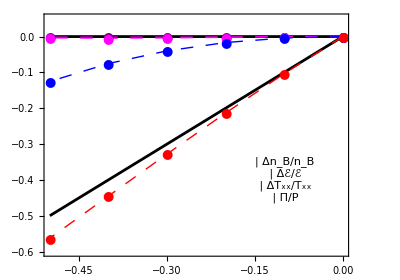

{a→-0.373515,b→0.194867,c→-0.12021,d→0.,e→0.}

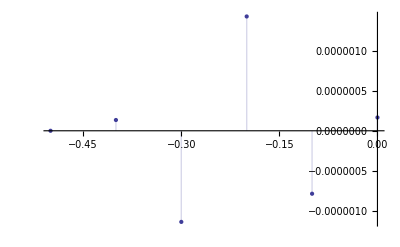

```mathematica
(* Π *)

T = 0.165;
μB =0.126; 

frac=Table[-0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,-0.000,-0.0020602,-0.0036116,-0.0044516,-0.0036247};

PioverPdata = {0.0,-0.10355,-0.21335,-0.3279,-0.44519,-0.56263};

ΔTxxoverTxxdata = {0.0,-0.0039419,-0.016693,-0.03985,-0.075312,-0.12525};


style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};


legend1=Panel[Grid[{{Graphics[{Purple,Disk[]},ImageSize->10],Style["Δn_B/n_B",FontSize->18,FontFamily->"Times"]},{Graphics[{RGBColor[1,0,1],Disk[]},ImageSize->10],Style["Δℰ/ℰ",FontSize->18,FontFamily->"Times"]},
{Graphics[{RGBColor[0,0,1],Disk[]},ImageSize->10],Style["ΔT_xx/T_xx",FontSize->18,FontFamily->"Times"]},
{Graphics[{Red,Disk[]},ImageSize->10],Style["Π/P",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend2=Panel[Grid[{{Style["T_ch = 165 MeV",FontSize->18,FontFamily->"Times"]},{},
{Style["μ_B = 126 MeV",FontSize->18,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
PioverPplot = Table[{frac[[i]],PioverPdata[[i]]},{i,1,Length[frac]}];
ΔTxxoverTxxplot = Table[{frac[[i]],ΔTxxoverTxxdata[[i]]},{i,1,Length[frac]}];

pi1=Show[{{
Plot[{x,0.0},{x,-0.5,0},PlotRange->{-0.6,0.05},ImageSize->{450,400},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,Δϵoverϵplot,ΔTxxoverTxxplot,PioverPplot},PlotRange->{-0.6,0.05},Joined->True,ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{Purple,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{Blue,Thick,Dashing[Medium]},{Red,Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend1,{-0.1,-0.4}]},ImageSize->{400,300}]


(*Fit for the average pressure deviations*)
data=ΔTxxoverTxxplot;
model=a*x^2+b*x^3+c*x^4;
fit=FindFit[data,model,{a,b,c,d,e},x]
modelf=Function[{x},Evaluate[model/.fit]];
{tl,yl}=Transpose[data];
residuals=yl-Map[modelf,tl];
ListPlot[residuals,Filling->Axis,DataRange->{Min[tl],Max[tl]},PlotRange->{All}]
```

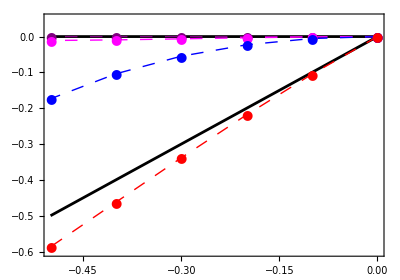

```mathematica
(* Π_*)

T = 0.140;
μB =0.417; 

frac=Table[-0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,-0.0009175,-0.0032568,-0.0063097,-0.009244,-0.011};

PioverPdata = {0.0,-0.10484,-0.21829,-0.33832,-0.46232,-0.58683};

ΔTxxoverTxxdata = {0.0,-0.005383,-0.022856,-0.054742,-0.10387,-0.17366};


style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};


legend1=Panel[Grid[{{Graphics[{Purple,Disk[]},ImageSize->10],Style["Δn_B/n_B",FontSize->18,FontFamily->"Times"]},{Graphics[{RGBColor[1,0,1],Disk[]},ImageSize->10],Style["Δℰ/ℰ",FontSize->18,FontFamily->"Times"]},
{Graphics[{RGBColor[0,0,1],Disk[]},ImageSize->10],Style["ΔT_xx/T_xx",FontSize->18,FontFamily->"Times"]},
{Graphics[{Red,Disk[]},ImageSize->10],Style["Π/P",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend2=Panel[Grid[{{Style["T_ch = 140 MeV",FontSize->18,FontFamily->"Times"]},{},
{Style["μ_B = 417 MeV",FontSize->18,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
PioverPplot = Table[{frac[[i]],PioverPdata[[i]]},{i,1,Length[frac]}];
ΔTxxoverTxxplot = Table[{frac[[i]],ΔTxxoverTxxdata[[i]]},{i,1,Length[frac]}];


(*Fit for the average pressure deviations*)
data=ΔTxxoverTxxplot;
model=a+b*x+c*x^2+0*x^3+0*x^4;
fit=FindFit[data,model,{a,b,c,d,e},x];
modelf=Function[{x},Evaluate[model/.fit]];
{tl,yl}=Transpose[data];
residuals=yl-Map[modelf,tl];
ListPlot[residuals,Filling->Axis,DataRange->{Min[tl],Max[tl]},PlotRange->{All}];

pi2=Show[{{
Plot[{x,0},{x,-0.5,0},PlotRange->{-0.6,0.05},ImageSize->{450,400},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,Δϵoverϵplot,ΔTxxoverTxxplot,PioverPplot},PlotRange->{-0.6,0.05},Joined->True,ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{Purple,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{Blue,Thick,Dashing[Medium]},{Red,Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},ImageSize->{400,330}]
```

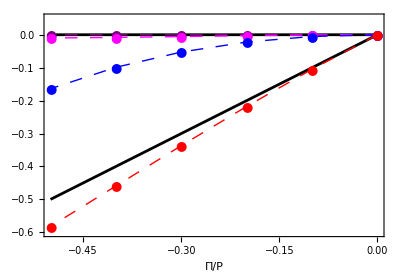

{a→-0.498684,b→0.235831,c→-0.155835,d→0.,e→0.}

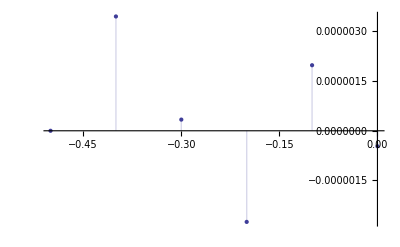

```mathematica
(* Π_*)

T = 0.120;
μB =0.548; 

frac=Table[-0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,-0.00078457,-0.0027965,-0.0054557,-0.008092,-0.0099288};

PioverPdata = {0.0,-0.10471,-0.21767,-0.33676,-0.45932,-0.58195};

ΔTxxoverTxxdata = {0.0,-0.0052348,-0.022083,-0.052514,-0.09887,-0.16389};


style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};


legend1=Panel[Grid[{{Graphics[{Purple,Disk[]},ImageSize->10],Style["Δn_B/n_B",FontSize->18,FontFamily->"Times"]},{Graphics[{RGBColor[1,0,1],Disk[]},ImageSize->10],Style["Δℰ/ℰ",FontSize->18,FontFamily->"Times"]},
{Graphics[{RGBColor[0,0,1],Disk[]},ImageSize->10],Style["ΔT_xx/T_xx",FontSize->18,FontFamily->"Times"]},
{Graphics[{Red,Disk[]},ImageSize->10],Style["Π/P",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend2=Panel[Grid[{{Style["T_ch = 120 MeV",FontSize->18,FontFamily->"Times"]},{},
{Style["μ_B = 548 MeV",FontSize->18,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
PioverPplot = Table[{frac[[i]],PioverPdata[[i]]},{i,1,Length[frac]}];
ΔTxxoverTxxplot = Table[{frac[[i]],ΔTxxoverTxxdata[[i]]},{i,1,Length[frac]}];

pi3=Show[{{
Plot[{x,0.0},{x,-0.5,0},PlotRange->{-0.6,0.05},ImageSize->{450,400},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,Δϵoverϵplot,ΔTxxoverTxxplot,PioverPplot},PlotRange->{-0.6,0.05},Joined->True,ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13},{●,13}},PlotStyle->{{Purple,Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{Blue,Thick,Dashing[Medium]},{Red,Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},ImageSize->{400,330},FrameLabel->Style["Π/P",FontFamily->"Times"]]


(*Fit for the average pressure deviations*)
data=ΔTxxoverTxxplot;
model=a*x^2+b*x^3+c*x^4;
fit=FindFit[data,model,{a,b,c,d,e},x]
modelf=Function[{x},Evaluate[model/.fit]];
{tl,yl}=Transpose[data];
residuals=yl-Map[modelf,tl];
ListPlot[residuals,Filling->Axis,DataRange->{Min[tl],Max[tl]},PlotRange->{All}]


(*I should put the equilibrium energy density, pressure and baryon density and an order of magnitude feeling*)
```

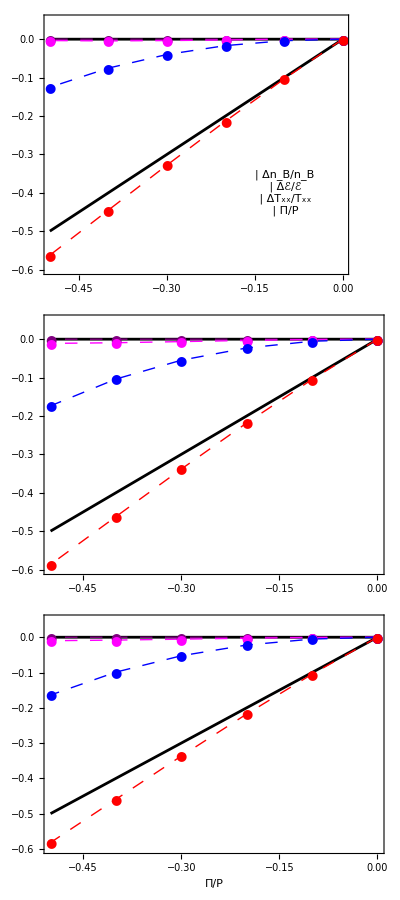

```mathematica
Pitotal=Grid[{{pi1},{pi2},{pi3}}]
```